```mathematica
GzmG0[z_,R_]:=Re[(π R^4 (√(1-(z/(2*R))^2) (2+(z/(2*R))^2)-(z/(2*R))^2 (-4+(z/(2*R))^2) Log[(z/(2*R))/(1+√(1-(z/(2*R))^2))]))]-2*Pi*R^4
```

```mathematica
Limit[GzmG0[z,R],z->Infinity, Assumptions->R>0]
```

-2 π R^4

```mathematica
NGzmG0[z_,R_,sl_,N_]:=N*(NIntegrate[Exp[-(1-l)^2/(2*sl^2)]/((√(π/2) sl (1+Erf[1/(√2 sl)])))*GzmG0[z*l^2,R]*l^2,{l,0,Infinity},MinRecursion->5])
```

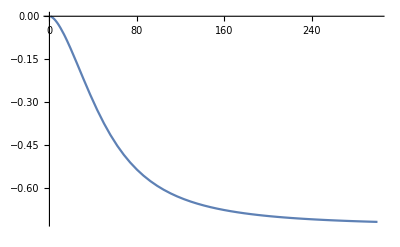

```mathematica
Plot[NGzmG0[z,100,0.4,1*10^(-9)],{z,1,300},PlotRange->Full]
```

```mathematica
Plot[NGzmG0[z,100,0.4,1*10^(-9)]/NGz[z,100,0.01,1*10^(-9)],{z,1,300},PlotRange->Full]
```

-Graphics-

```mathematica
NPz[z_,R_,sl_,N_]:=NIntegrate[Exp[-(1-l)^2/(2*sl^2)]/(√(π/2) sl (1+Erf[1/(√2 sl)]))*Exp[N*GzmG0[z*l^2,R]*l^2],{l,0,Infinity},MinRecursion->5,Method->"DoubleExponential"]
```

```mathematica
FullSimplify[Integrate[Exp[-(1-l)^2/(2*sl^2)]/(√(π/2) sl (1+Erf[1/(√2 sl)])),{l,0,Infinity},Assumptions->sl>0]]
```

1

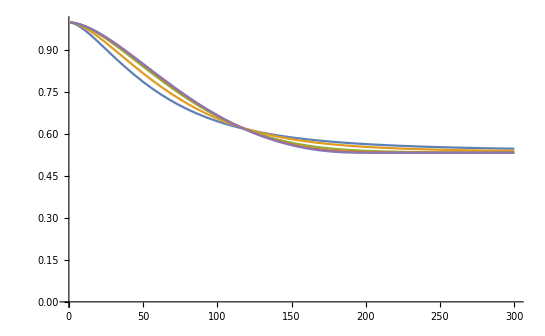

```mathematica
Plot[{NPz[z,100,0.3,1*10^(-9)],NPz[z,100,0.2,1*10^(-9)],NPz[z,100,0.1,1*10^(-9)],NPz[z,100,0.05,1*10^(-9)],NPz[z,100,0.01,1*10^(-9)]},{z,1,300},PlotRange->{0,1}]
```

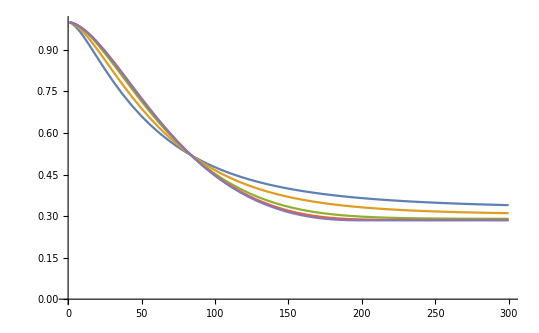

```mathematica
Plot[{NPz[z,100,0.3,2*10^(-9)], NPz[z,100,0.2,2*10^(-9)],NPz[z,100,0.1,2*10^(-9)],NPz[z,100,0.05,2*10^(-9)],NPz[z,100,0.01,2*10^(-9)]},{z,1,300},PlotRange->{0,1}]
```

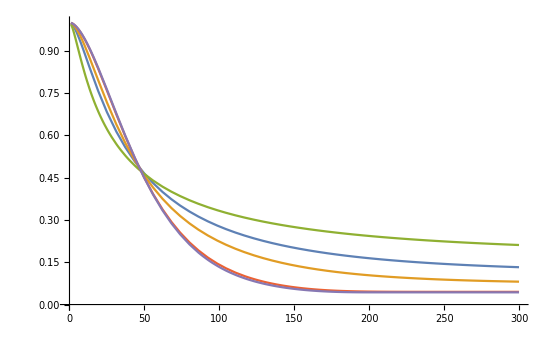

```mathematica
Plot[{NPz[z,100,0.3,5*10^(-9)],NPz[z,100,0.2,5*10^(-9)],NPz[z,100,0.5,5*10^(-9)],NPz[z,100,0.05,5*10^(-9)],NPz[z,100,0.01,5*10^(-9)]},{z,1,300},PlotRange->{0,1}]
```

```mathematica
N[NPz[1,100,0.04,3*10^(-9)]]
```

0.999424

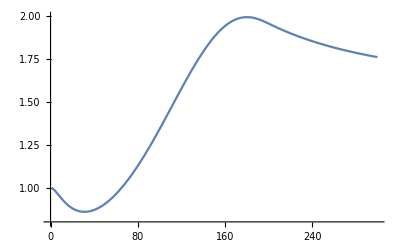

```mathematica
Plot[NPz[z,100,0.4,3*10^(-9)]/NPz[z,100,0.01,3*10^(-9)],{z,1,300},PlotRange->{0.8,2}]
```

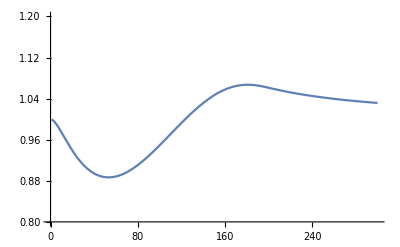

```mathematica
Plot[NPz[z,100,0.4,1*10^(-9)]/NPz[z,100,0.01,1*10^(-9)],{z,1,300},PlotRange->{0.8,1.2}]
```

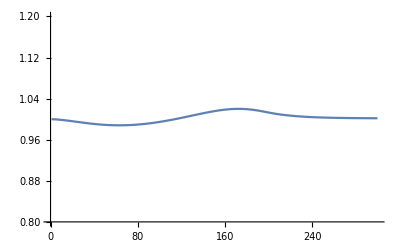

```mathematica
Plot[NPz[z,100,0.1,1*10^(-9)]/NPz[z,100,0.01,1*10^(-9)],{z,1,300},PlotRange->{0.8,1.2}]
```

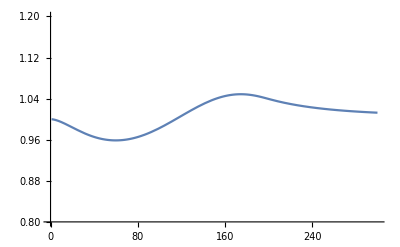

```mathematica
Plot[NPz[z,100,0.2,1*10^(-9)]/NPz[z,100,0.01,1*10^(-9)],{z,1,300},PlotRange->{0.8,1.2}]
```

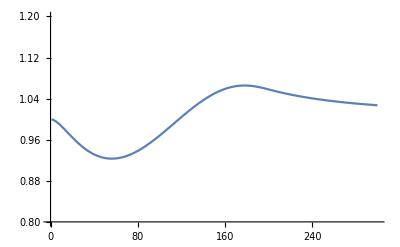

```mathematica
Plot[NPz[z,100,0.3,1*10^(-9)]/NPz[z,100,0.01,1*10^(-9)],{z,1,300},PlotRange->{0.8,1.2}]
```

```mathematica
Plot3D[NPz[55,100.,sl,x*10^(-9)]/NPz[55,100.,0.01,x*10^(-9)],{sl,0.1,0.4},{x,0.1,5}]
```

-Graphics3D-

```mathematica
N[NPz[55.,100.,0.4,1.5*10^(-9)]]
```

0.665406

```mathematica
Needs["GUIKit`"]
```

```mathematica
ExplorerRun[]:=GUIRun["Wolfram/NIntegrateExplorer/ExplorerGUI"]
```

```mathematica
ExplorerRun[]
```

⁃GUIObject⁃